## Generate n-partite Network

Functions

```mathematica
SetDirectory[NotebookDirectory[]]
<<PajaroLocoPublic`
nonMigratoryForce=1000;
CalculateEuclideanDistances[coordinates_]:=Table[N[EuclideanDistance[coordinates[[i]],#]]&/@coordinates,{i,1,coordinates//Length }]
CalculateMigrationProbabilities[distancesMatrix_,nonMigratoryForce_]:=N[(#/Total[#])]&/@ReplaceAll[1/distancesMatrix//Quiet,ComplexInfinity->nonMigratoryForce]
ListPlotPoints[points_]:=ListPlot[points,
Frame->True,
Axes->True,
FrameStyle->Thickness[.005],
ImageSize->800,
FrameTicksStyle->None,
PlotStyle->PointSize[.025],
AspectRatio->1
]Options[EdgesStyleList2]:={LineThickness->.004,VariableStyle->"Both"}
EdgesStyleList2[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{ColorData[{"LakeColors","Reverse"}][vertexSyllableList[[i]][[2]]],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Black,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{ColorData[{"LakeColors","Reverse"}][vertexSyllableList[[i]][[2]]],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
edgeshape[e_,___]:={Arrowheads[{{.0075,.5}}],Arrow[e]}
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,Frame->False,FrameStyle->Thick,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
Frame->OptionValue[Frame],
FrameStyle->OptionValue[FrameStyle],
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding],
PerformanceGoal->"Speed"
]
]
Themes`AddThemeRules["RandomPointsPlot",
AspectRatio->1,
Frame->True,
FrameLabel->(Style[#,20]&/@{"x (meters)","y (meters)"}),
FrameTicksStyle->20,
FrameStyle->Thick,
FrameTicks->{{None,All},{None,All}},
PlotStyle->Directive[PointSize[.02],Opacity[.75]],
AxesStyle->Directive[{Opacity[.25],Thick,Gray}]
]
Themes`AddThemeRules["RandomPointsMatrix",
AspectRatio->1,
Frame->True,
FrameStyle->Thick,
FrameTicks->{{None,None},{None,None}},
ColorFunction->"LakeColors",
AxesStyle->Directive[{Opacity[.25],Thick,Gray}]
]
DistributionIntoKernel[distribution_,center_,n_]:=Table[center+{Re[#],Im[#]}&[RandomReal[distribution] ⅇ^(ⅈ RandomReal[{0,2π}])],{n}]
MapDistributionParametersOnPoints[distribution_,centers_,n_]:=Join@@(DistributionIntoKernel[distribution,#,n]&/@centers)
SphereDistance[{ϕ1_,θ1_},{ϕ2_,θ2_},r_]:=r InverseHaversine[Haversine[ϕ1-ϕ2]+Cos[ϕ1]Cos[ϕ2]Haversine[θ1-θ2]]
SphereDistanceBetweenPoints[sphericalCoordinates1_,sphericalCoordinates2_]:=Module[{tuple},
tuple={
CoordinateTransformData["Cartesian"->"Spherical", "Mapping",sphericalCoordinates1],
CoordinateTransformData["Cartesian"->"Spherical", "Mapping",sphericalCoordinates2]
};
SphereDistance[{tuple[[1,2]],tuple[[1,3]]},{tuple[[2,2]],tuple[[2,3]]},tuple[[1,1]]]
]
SmoothHistogramPlot[sampledCoordinatesLayer_,{imageSize_,imagePadding_},plotRange_]:=SmoothHistogram[sampledCoordinatesLayer,
PlotStyle->Directive[{Thickness[.01],Opacity[.5]}],
ImageSize->imageSize,
PlotRange->{plotRange[[1]],plotRange[[2]]},
AspectRatio->.075,
Axes->False,
FrameTicks->{None,None},
Filling->Bottom,
FrameLabel->None,
ImagePadding->imagePadding,
ImageSize->imageSize,
PlotTheme->"RandomPointsPlot"
]
ListPlotScatter[clusteredCoordinates_,{imageSize_,imagePadding_},plotRange_]:=
ListPlot[clusteredCoordinates,
FrameTicks->Automatic,
BaseStyle->15,
LabelStyle->Directive[10],
FrameLabel->{{None,Rotate["y [meters]",180Degree]},{None,"x [meters]"}},
PlotRange->{plotRange[[1]],plotRange[[1]]},
PlotTheme->"RandomPointsPlot",
PlotStyle->Directive[{PointSize[.025],Opacity[.5]}],
ImageSize->imageSize,
ImagePadding->imagePadding
]
```

/Users/sanchez.hmsc/Documents/GitHub/MoNeT/Dev/HectorSanchez/PartiteNetworks

RandomPointsPlot

RandomPointsMatrix

```mathematica
"/Users/sanchez.hmsc/Documents/GitHub/MGDrivE/BRInE"
```

/Users/sanchez.hmsc/Documents/GitHub/MGDrivE/BRInE

```mathematica
"RandomPointsPlot"
```

RandomPointsPlot

```mathematica
"RandomPointsMatrix"
```

RandomPointsMatrix

Inputs

```mathematica
{citiesNumber,coordinatesRange}={30,100};
(*Classes number should be equal to the dimension of the penalizations matrix*)
classesNumber=5;
penalizationsMatrix={
{0,.8,.2,0,0},
{.1,0,.9,0,0},
{0,0,0,1,0},
{.85,.1,.25,0,.25},
{1,0,0,0,0}
};
```

Generate Random Spatial Setting

ListPlot::prng: Value of option PlotRange -> {{-75+min,75+max},{-75+min,75+max}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

MatrixPlot::mat0: Argument eucledianDistances at position 1 is not a matrix.

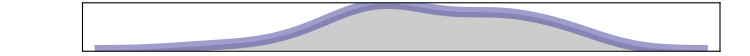
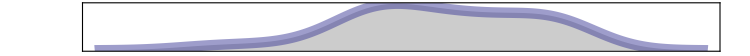
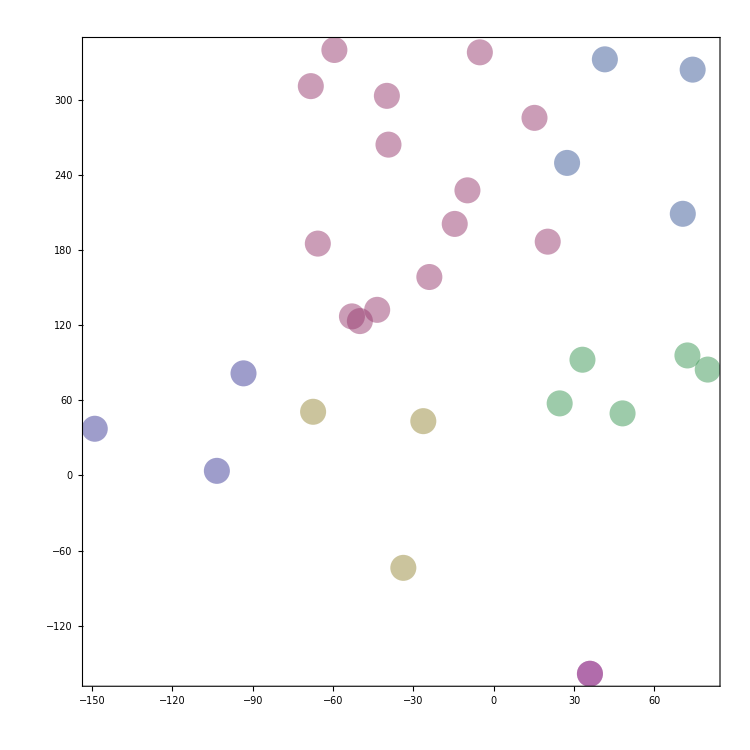
| -Graphics- | 
-Graphics- | -Graphics- |  | MatrixPlot[eucledianDistances,ColorFunction→LakeColors,ImageSize→750]

```mathematica
(*User Input*)
{imageSize, imagePadding, plotRange} = {750,50,{{min-75,max+75},{0,.01}}};
(*Generate Random Coordinates*)
sampledCoordinates=citiesDummy = Accumulate[RandomReal[{-coordinatesRange,coordinatesRange}, {citiesNumber, 2}]];
names = ToString /@ Range[citiesDummy // Length];
pops = RandomInteger[1000, citiesDummy // Length];
cities = Transpose[{names, citiesDummy, pops}];
distances = CalculateEuclideanDistances[citiesDummy];
clusteredCoordinates = FindClusters[sampledCoordinates, Method -> "NeighborhoodContraction"];
migration = CalculateMigrationProbabilities[distances, 1000];
(*Generate Plots*)
histograms = SmoothHistogramPlot[#, {imageSize, imagePadding}, plotRange] & /@ Transpose[sampledCoordinates];
scatter = ListPlotScatter[clusteredCoordinates, {imageSize, imagePadding}, plotRange];
grid = Grid[{
    {"", Rotate[histograms[[1]] // Show[#, ImagePadding -> {{imagePadding, imagePadding}, {0, 0}}] &, 0 Degree], ""},
    {Rotate[histograms[[2]] // Show[#, ImagePadding -> {{imagePadding, imagePadding}, {0, 0}}] &, 90 Degree], scatter // Show[#, ImagePadding -> {{imagePadding, imagePadding}, {imagePadding, imagePadding}}] &, ""}
    }];
spatialPlot= Grid[{{grid, MatrixPlot[eucledianDistances, ColorFunction -> "LakeColors", ImageSize ->imageSize]}}]
```

Partition Setting

```mathematica
(*Random Sample Cities to Class*)
cityType=RandomChoice[Range[classesNumber],citiesNumber]
```

{4,5,3,3,2,5,5,4,2,1,3,3,3,3,1,4,1,4,1,2,5,1,5,4,5,4,4,1,1,5}

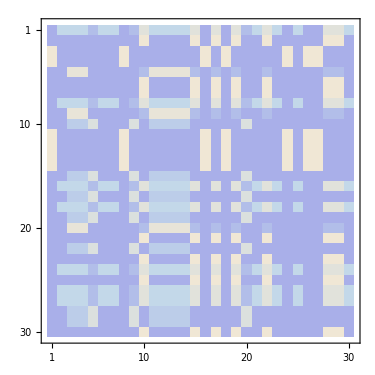

```mathematica
{cityType[[1]],#}&/@cityType;
penalizationsMask=Table[penalizationsMatrix[[i,#]]&/@cityType,{i,cityType}];
penalizationsMaskPlot=penalizationsMask//MatrixPlot[#,ColorFunction -> "LakeColors", ImageSize ->imageSize/2]&
```

Mask Kernel

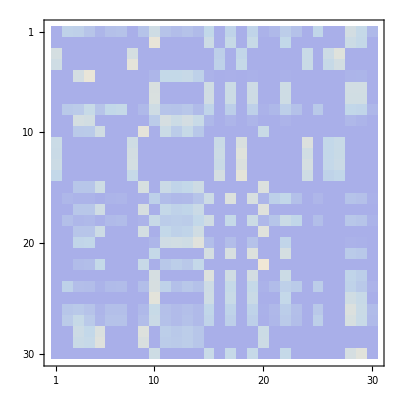

```mathematica
normalizedMaskedMatrix=(#/Total[#])&/@(penalizationsMask*migration);
stylesSwatch=Directive[Opacity[1],Lighter[#,.6],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@ColorData[1,"ColorList"][[1;;classesNumber]];
stylesList=(ToString[#[[1]]]->stylesSwatch[[#[[2]]]])&/@Transpose[{Range[cityType//Length],cityType}];
normalizedMaskedMatrixPlot=normalizedMaskedMatrix//MatrixPlot[#,ColorFunction->"LakeColors"]&
```

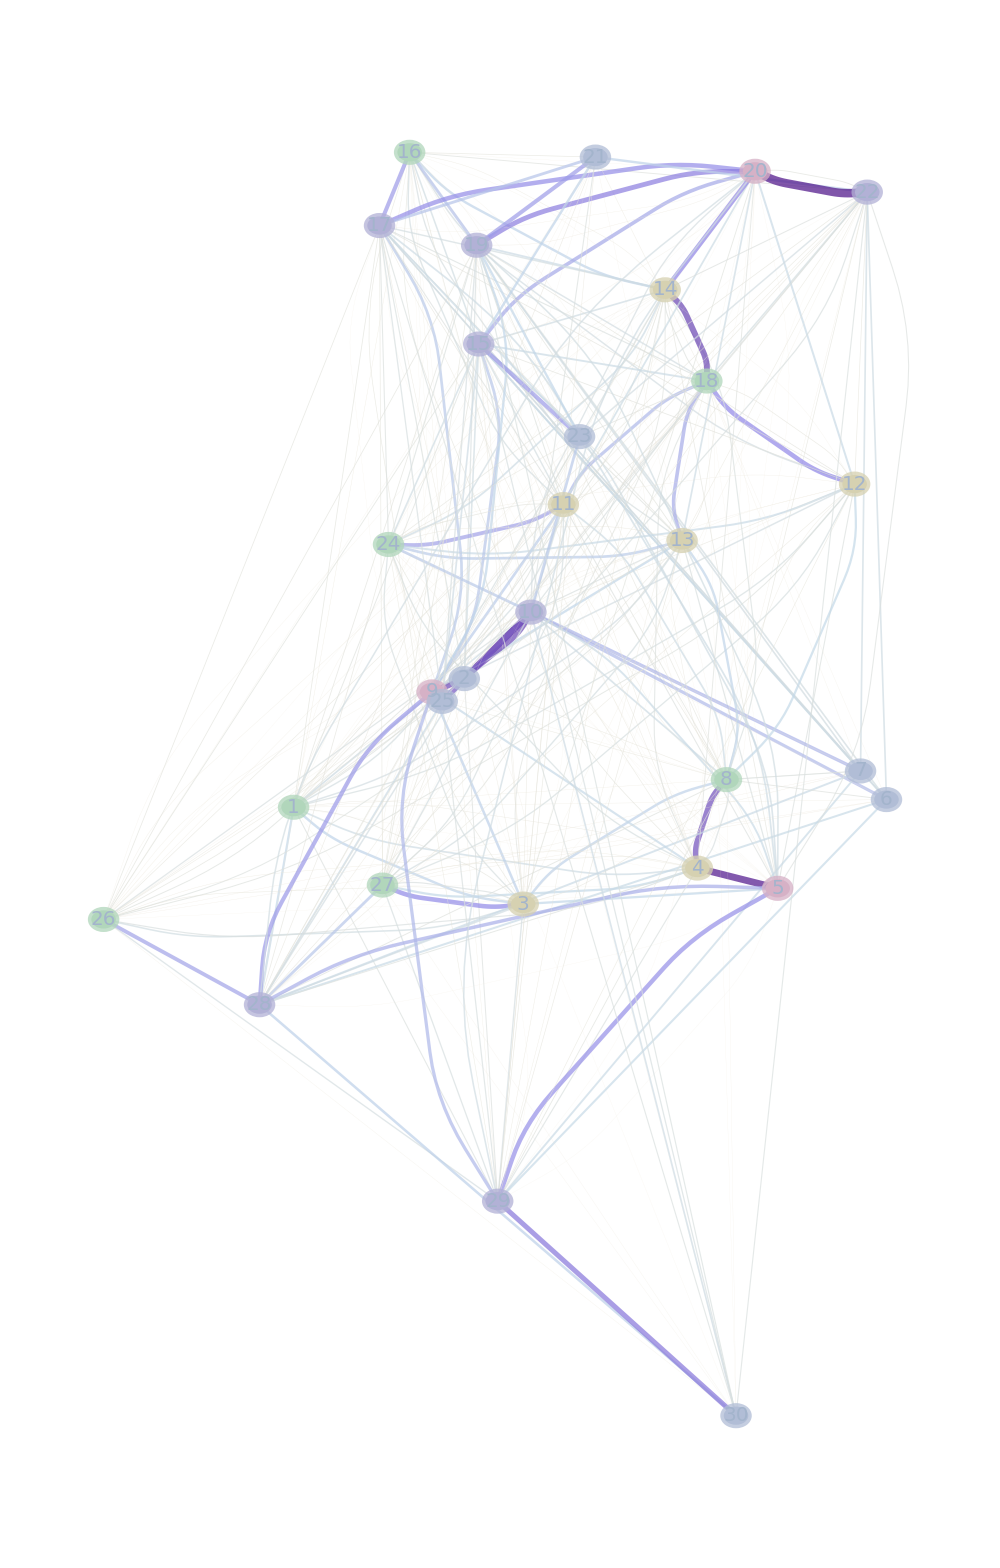

```mathematica
edgeshape2[e_,___]:={Arrowheads[{{.015,.5}}],Arrow[e]}
graph = GraphTransitionsFrequenciesWithMax[
  {
Chop[normalizedMaskedMatrix],
ToString /@ Range[Length[normalizedMaskedMatrix]]
   }, .5,
 VertexStyle -> stylesList,
VertexCoordinates -> sampledCoordinates,
VertexSize -> 1.5,
VertexLabelStyle->20,
ImageSize -> 1000,
LineThickness -> .005,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both"
  ]
```

Export

```mathematica
SetDirectory[NotebookDirectory[]]
Export["nPartiteAdjMatrix.csv",normalizedMaskedMatrix]
Export["normalizedMakedMatrix.pdf",normalizedMaskedMatrixPlot]
Export["penalizationsMatrix.pdf",penalizationsMaskPlot]
Export["spatialPlot.pdf",spatialPlot]
Export["network.pdf",graph]
```

/Users/sanchez.hmsc/Documents/GitHub/MoNeT/Dev/HectorSanchez/PartiteNetworks

nPartiteAdjMatrix.csv

normalizedMakedMatrix.pdf

penalizationsMatrix.pdf

spatialPlot.pdf

network.pdf